# Calculation for DC offset and contrast of an optical lattice reflecting off uncoated substrate

This notebook was predominantly made because the optical lattice used for the axial confinement in the greiner lab Rb quantum gas microscope reflects off an uncoated substrate that has imperfect reflection and variable lattice spacing depending upon the angle. There are actually two of these installed with different angles that also have different DC light shifts and scattering rates to be accounted for

## Axial Lattice Scattering? (Remember, it is mostly DC Light)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Subscript[λ, rb]=780.241209686 10^-9;
Subscript[λ, laser]=758 10^-9;
Subscript[γ, rb] = 2π  6.065 10^6;
Subscript[f, laser]=c/Subscript[λ, laser];
Subscript[f, rb]=c/Subscript[λ, rb];
Subscript[δ, rb]= 2 π(Subscript[f, laser]-Subscript[f, rb]);

Wo=100 10^-6;
zr[wo_]:=(π wo^2)/Subscript[λ, laser]
Wr[z_,wo_]:=wo √(1+(z/zr[wo]))
Ilatt[z_,r_,wo_,po_]:=(2 po)/(wo^2 π)(wo/Wr[z,wo])^2 Exp[(- 2 r^2)/Wr[z,wo]^2]
```

```mathematica
Subscript[Γ, scAxial][r_,z_,wo_,po_]:=(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[f, laser]/Subscript[f, rb])^3(Subscript[γ, rb]/(-Subscript[δ, rb])+Subscript[γ, rb]/(2 (2 π Subscript[f, laser])+ Subscript[δ, rb]))Ilatt[z,r,wo,po]
```

```mathematica
Subscript[λ, rb]=780.241209686 10^-9;
Subscript[λ, laser]=758 10^-9;
Subscript[γ, rb] = 2π  6.065 10^6;
Subscript[f, laser]=c/Subscript[λ, laser];
Subscript[f, rb]=c/Subscript[λ, rb];
Subscript[δ, rb]= 2 π(Subscript[f, laser]-Subscript[f, rb]);
Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 0.1)/((100 10^-6)^2 π)]
```

0.525897

#### Expected scattering from naive calculation given different aspect ratios of power in dc offset of axial lattice

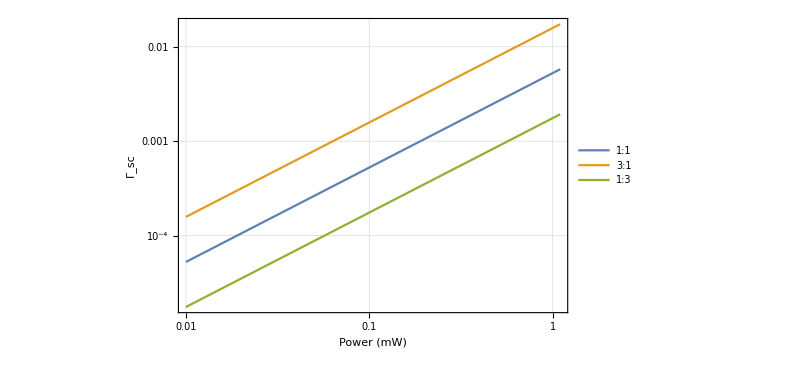

```mathematica
LogLogPlot[{Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 P/1000)/((100 10^-6)(100 10^-6)π)],
Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 P/1000)/((100 10^-6)(100 10^-6/3)π)],
Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 P/1000)/((100 10^-6)(3 100 10^-6)π)]}
,{P ,0.01,1.1},
GridLines-> Automatic,
Frame -> True,
PlotLegends-> {"1:1","3:1","1:3"},
ImageSize-> 600,
FrameLabel-> {"Power (mW)","Γ_sc","Single-Photon Axial Scattering Rate, 100um waist" }]
```

### Fresnel Coefficients (in intensity) depending on coming two indices of reflection and angle

```mathematica
Rs[n1_,n2_,θ_]:=Abs[(n1 Cos[θ]-n2 √(1-(n1/n2 Sin[θ])^2))/(n1 Cos[θ]+n2 √(1-(n1/n2 Sin[θ])^2))]^2
Rp[n1_,n2_,θ_]:=Abs[(n1 √(1-(n1/n2 Sin[θ])^2)-n2 Cos[θ])/(n1 √(1-(n1/n2 Sin[θ])^2)+n2 Cos[θ])]^2
```

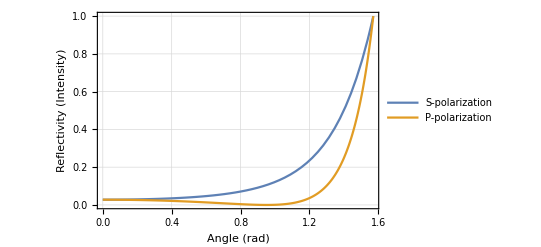

```mathematica
Plot[{Rs[1,1.4,x],Rp[1,1.4,x]},{x,0,π/2},
PlotRange-> {{0, π/2},{0,1}},
Frame-> True,
GridLines-> Automatic,
FrameLabel-> {"Angle (rad)","Reflectivity (Intensity)","Fresnel Coefficients"},
PlotLegends-> {"S-polarization","P-polarization"}]
```

#### Fresnel Coefficients estimated for known angles in lattice

In reality, this is calculated in reverse where the easier thing to measure is the spacing of the lattice in the axial direction. Then, knowing the wavelength of the light, it is easy to figure out the angle and therefore the contrast of the light and DC shift. The two known approximate angles are ~2° and ~15°

```mathematica
√Rs[1,1.45,π/2((90-15)/90)]
Rp[1,1.45,π/2((90-15)/90)]
```

0.613774

0.109231

```mathematica
√Rs[1,1.45,π/2((90-2)/90)]
Rp[1,1.45,π/2((90-14.5)/90)]
```

0.935698

0.118593

A plot giving the lattice spacing versus the angle away from the normal vector away from the substrate. This diverges off to infinity as the angle becomes parallel to the substrate, so we just plot this on a semilog plot.

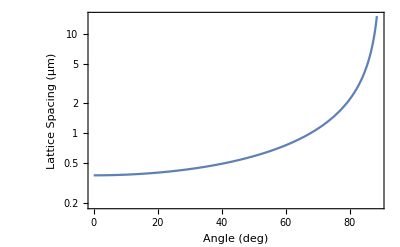

```mathematica
LogPlot[0.758/2/Cos[x  π /180],{x,0.01,90},
PlotRange-> {{0.01,89},{0.765/4,15}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Lattice Spacing (μm)","Z-Confining Lattice"}]
```

Zoomed in view of same plot as to more easily pinpoint the angle of the lattice angle from the known/measured spacing
The “big lattice” in the experiment is approximately ~10μm = ~87.75°

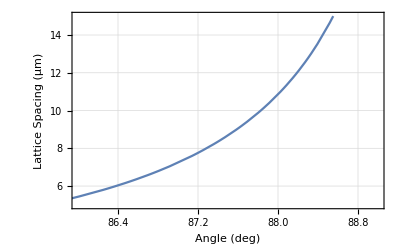

```mathematica
Plot[{0.758/2/Cos[x  π /180]},{x,0.01,90},
PlotRange-> {{86,89},{5,15}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Lattice Spacing (μm)","Z-Confining Lattice (Big Lattice Region)"}]
```

This is the same plot to extract the angle form the tighter confining lattice known as the “axial lattice” in the experiment
~1.5μm = ~75°

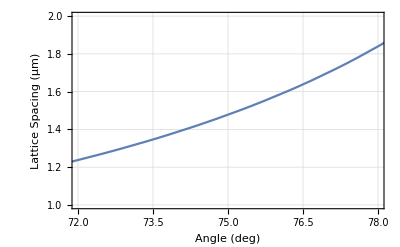

```mathematica
Plot[0.765/2/Cos[x  π /180],{x,0.01,90},
PlotRange-> {{72,78},{1,2}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Lattice Spacing (μm)","Z-Confining Lattice (Axial Lattice Region)"}]
```

### Plot the optical potential of the two different axial confining lattices given the estimated angles

These plots show both the contrast, offset, and spacing from the different angles. Notice that the minima align at ~9μm and that the contrast and offset between the two are quite different. The axial lattice offset would provide an extra heating mechanism in this lattice that is different from the typical heating expected in an optical lattice that typically assumes full contrast.

```mathematica
Alatt[th_]:=0.730/2/Cos[th π /180]
Manipulate[
Plot[{Abs[1/(√2)Exp[-I x 2 π/Alatt[thaxial]/2 - I π/2]+1/(√2)√Rs[1,1.45,π/2(thaxial/90)] Exp[I x 2 π/Alatt[thaxial]/2 +I π/2]]^2,
Abs[1/(√2)Exp[-I x 2 π/Alatt[thbig]/2 - I π/2]+1/(√2) √Rs[1,1.45,π/2(thbig/90)] Exp[I x 2 π/Alatt[thbig]/2+ I π/2]]^2},{x,0,11},
PlotRange-> {{0,11},{0,2}},
PlotLegends-> {"Axial Lattice","Big Lattice"},
ImageSize-> 600,
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Spacing (μm)","Depth (Itensity), 1-normalized to incoming power","Axial Confining Lattices"}],
{{thaxial,75},0,90},
{{thbig,87.5},0,90}]
```

```mathematica
(*
ur=Table[NIntegrate[Abs[Subscript[ψ, wv][x,n,0]]^2 Abs[Subscript[ψ, wv][x,n,1]]^2,{x,-4 π, 4 π}]/NIntegrate[Abs[Subscript[ψ, wv][x,n,0]]^2 Abs[Subscript[ψ, wv][x,n,0]]^2,{x,- 4 π,4 π}],{n,1,25}];
ListPlot[ur]
*)
```

```mathematica
BigLattDC=(1+Rs[1,1.45,π/2((90-2.32)/90)]-2.*(√Rs[1,1.45,π/2((90-2.32)/90)]))200;
AxialLattDC=(1+Rs[1,1.45,π/2((90-15)/90)]-2.*(√Rs[1,1.45,π/2((90-15)/90)]))200;
```

### Comparison of scattering rates from all sources and also in combination

```mathematica
GSCBLUEDPhys[n_]:=NIntegrate[n (1-Cos[x π]^2)( 2 π 1.24 10^3)Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}];
GSCBLUEDPin[n_]:=NIntegrate[n (1-Cos[x π]^2) (2 π 1.24 10^3)Subscript[γ, rb]/(2 π 60 10^9)(Subscript[ψ, wv][x,n,0])^2,{x,-1,1}];
GSCBLUEDBigPhys[n_]:=NIntegrate[n (1-Cos[x π]^2) (2 π  1.24 10^3)(0.68/9.2)^2 Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}];
GSCBLUEDAxPhys[n_]:=NIntegrate[n (1-Cos[x π]^2) (2 π  1.24 10^3)(0.68/1.5)^2 Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}];
```

```mathematica
BigLatticeSPRate=Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 BigLattDC/1000)/((150 10^-6)(150 10^-6/2.6)π)];
AxialLatticeSPRate=Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 AxialLattDC/1000)/((150 10^-6)(150 10^-6)π)];
PhysLat2D1Rate=GSCBLUEDPhys[60];
PhysLat2D2Rate=GSCBLUEDPhys[8];
PhysBigLatRate=GSCBLUEDBigPhys[9404];
PhysAxLatRate = GSCBLUEDAxPhys[250];

Rin2D1=0.0002;
Rin2D1=0;
Rin2D2=0.001;
Rin2D2=0;
```

```mathematica
Subscript[Γ, TotalBig]=BigLatticeSPRate+PhysLat2D1Rate+PhysLat2D2Rate+PhysBigLatRate
```

0.0123788

```mathematica
Subscript[Γ, TotalAxial]=AxialLatticeSPRate+PhysLat2D1Rate+PhysLat2D2Rate+PhysAxLatRate
```

0.0768325

```mathematica
N[1/0.0768]
```

13.0208

```mathematica
N[1/15]
```

0.0666667

3.05186

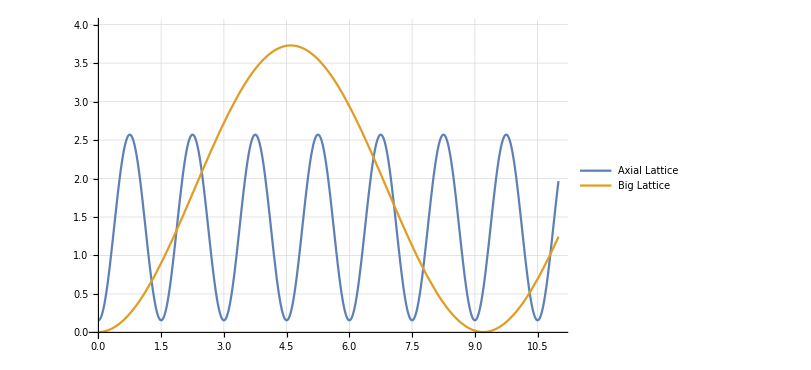

```mathematica
(0.765)/2/Sin[7.2 /90 * π/2]
Plot[{Abs[Exp[-I x 2 π/1.5/2 - I π/2]+√Rs[1,1.4,π/2((90-14.5)/90)] Exp[I x 2 π/1.5/2 +I π/2]]^2,
Abs[Exp[-I x 2 π/9.2/2 - I π/2]+√Rs[1,1.4,π/2((90-2)/90)] Exp[I x 2 π/9.2/2+ I π/2]]^2},{x,0,11},
PlotRange-> {{0,11},{0,4}},
PlotLegends-> {"Axial Lattice","Big Lattice"},
ImageSize-> 600,
GridLines-> Automatic]
```

### DC offset given angle of incidence

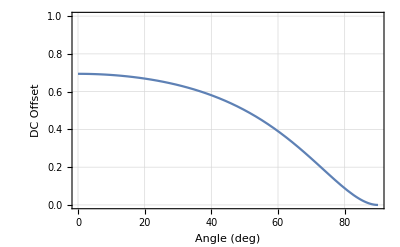

```mathematica
rfield[th_]:=√Rs[1,1.4,π/2(th/90)]
Plot[1+rfield[th]^2-2 rfield[th],{th,0,90},
PlotRange-> {{0,90},{0,1}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","DC Offset","DC Offset from Fresnel Coefficient Reflection"}]
```

### Contrast of optical lattice formed given angle of incidence

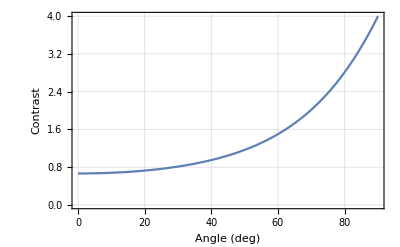

```mathematica
Plot[ 4 rfield[th],{th,0,90},
PlotRange-> {{0,90},{0,4}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Contrast","Contrast from Fresnel Coefficient Reflection"}]
```

### Section in progress: estimated entropy growth in time from scattering of bose-hubbard system that leads to doublon-hole pair formation

```mathematica
Pones[n_,t_,g_]:=(n Exp[-n g t]+(1-Exp[- n g t])(n-2))/n
Phole[n_,t_,g_]:=(1-Exp[- n g t])/n
Pdoublon[n_,t_,g_]:=(1-Exp[- n g t])/n
```

```mathematica
SVN[n_,t_,g_]:=-Pones[n,t,g]Log[Pones[n,t,g]]-Phole[n,t,g]Log[Phole[n,t,g]]-Pdoublon[n,t,g]Log[Pdoublon[n,t,g]]
```

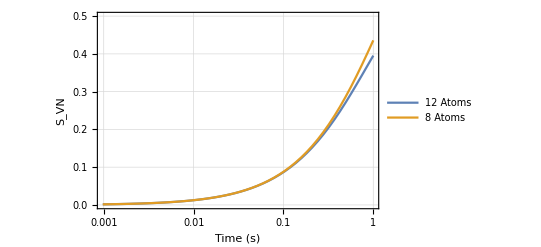

```mathematica
LogLinearPlot[{SVN[12,t,0.0768],{SVN[8,t,0.0768]}},{t,0,1},
GridLines-> Automatic,
PlotRange-> {{0,1}{0,0.5}},
Frame-> True,
PlotLegends-> {"12 Atoms","8 Atoms"},
FrameLabel-> {"Time (s)","S_VN","Entropy Growth from Scattering? γ=0.0768 Hz"}]
```